# Tension of the E_G statistic and RSD data with Planck/ΛCDM and implications for weakening gravity. Numerical Analysis and Construction Figures File

## Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
(* In order to use the Needs["ErrorBarLogPlots`"] command you need to install the "Error Bar Log Plots" package which can be installed directly from the zip file "ErrorBarLogPlots.zip" or you can download it from http://library.wolfram.com/infocenter/MathSource/6747/*)

Needs["ErrorBarLogPlots`"]
Off[General::"obspkg",NIntegrate::"inumr",NIntegrate::ncvb,CompiledFunction::cflist,ListInterpolation::inhr,FindMinimum::lstol,Part::partw,NonlinearModelFit::cvmit];
```

## Parameter values

```mathematica
ClearAll["Global`*"] 
Clear["Global`*"] 

(* Planck parameter Values for Planck18 *)

ompl=0.3153;
nn=2;
mm=2 ;
omplerr=0.0073;
h0pl=0.6727;
h0plerr=0.0066;
σ8pl=0.8111;
σ8plerr=0.006;
```

## Datasets

```mathematica
(* Data fσ8  *)

datafσ8={{0.02,0.314,0.048},{0.25,0.3512,0.0583},{0.44,0.413,0.08},{0.6,0.39,0.063},{0.73,0.437,0.072},{0.18,0.36,0.09},{0.15,0.49,0.145},{0.1,0.37,0.13},{1.4,0.482,0.116},{0.38,0.497,0.045},{0.51,0.458,0.038},{0.61,0.436,0.034},{1.05,0.28,0.08},{0.32,0.427,0.056},{0.727,0.296,0.0765},{0.02,0.428,0.0465},{0.001,0.505,0.085},{0.31,0.384,0.083},{0.36,0.409,0.098},{0.4,0.461,0.086},{0.44,0.426,0.062},{0.48,0.458,0.063},{0.52,0.483,0.075},{0.56,0.472,0.063},{0.59,0.452,0.061},{0.64,0.379,0.054},{0.978,0.379,0.176},{1.23,0.385,0.099},{1.526,0.342,0.07},{1.944,0.364,0.106},{0.60,0.49,0.12},{0.86,0.46,0.09},{0.57,0.501,0.051},{0.03,0.404,0.0815},{0.72,0.454,0.139}} ;
(* Data fσ8 with fiducial cosmology *)

datafσ8fid={{0.02,0.314,0.048,0.266},{0.25,0.3512,0.0583,0.25},{0.44,0.413,0.08,0.27},{0.6,0.39,0.063,0.27},{0.73,0.437,0.072,0.27},{0.18,0.36,0.09,0.27},{0.15,0.49,0.145,0.31},{0.1,0.37,0.13,0.3},{1.4,0.482,0.116,0.27},{0.38,0.497,0.045,0.31},{0.51,0.458,0.038,0.31},{0.61,0.436,0.034,0.31},{1.05,0.28,0.08,0.308},{0.32,0.427,0.056,0.31},{0.727,0.296,0.0765,0.31},{0.02,0.428,0.0465,0.3},{0.001,0.505,0.085,0.31},{0.31,0.384,0.083,0.307},{0.36,0.409,0.098,0.307},{0.4,0.461,0.086,0.307},{0.44,0.426,0.062,0.307},{0.48,0.458,0.063,0.307},{0.52,0.483,0.075,0.307},{0.56,0.472,0.063,0.307},{0.59,0.452,0.061,0.307},{0.64,0.379,0.054,0.307},{0.978,0.379,0.176,0.31},{1.23,0.385,0.099,0.31},{1.526,0.342,0.07,0.31},{1.944,0.364,0.106,0.31},{0.60,0.49,0.12,0.31},{0.86,0.46,0.09,0.31},{0.57,0.501,0.051,0.307},{0.03,0.404,0.0815,0.3121},{0.72,0.454,0.139,0.31}} ;
```

```mathematica
(* Data  Eg(z)*)

dataeg={{0.267,0.43,0.13},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.57,0.3,0.07},{0.6,0.16,0.09},{0.86,0.09,0.07}};

dataegb={{0.267,0.43,0.13},{0.305,0.27,0.08},{0.32,0.4,0.09},{0.554,0.26,0.07},{0.57,0.31,0.06},{0.575,0.3,0.07},{0.6,0.16,0.09},{0.86,0.09,0.07}};
```

## Theoretical Expressions

```mathematica
(* The fσ8  and the Subscript[E, G] observables *)

H[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)))
dLh[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)])
amin=0.001;

Geff[a_,ga_,n_]:=1+ga(1-a)^n-ga(1-a)^(2n);
Gl[z_,gb_,m_]:=1+gb(z/(1+z))^m-gb(z/(1+z))^(2m);

dsol[om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=(dsol[om,w,ga,n]=Module[{a},NDSolve[{-((3 om d[a] Geff[a,ga,n])/(2 a^5  H[a,w,om]^2))+d'[a] (3/a+D[H[a,w,om],a]/H[a,w,om])+d''[a]==0,d[amin]==amin,d'[amin]==1},d,{a,amin,1}][[1]]])

Da[a_,om_,w_,ga_,n_]:=d[a]/.dsol[om,w,ga,n]
fa[aa_,om_,w_,ga_,n_]:=a d'[a]/d[a]/.a->aa/.dsol[om,w,ga,n]

fσ8geff[a_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->a
fσ8z[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->1/(1+z)

ffz[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=fa[aa,om,w,ga,n]/.aa->1/(1+z)

ratio1[z_,w_,om_,omfid_]:=((H[a,w,om] dLh[a,om,w])/(H[a,-1,omfid] dLh[a,omfid,-1]))^(-1)/.a->1/(1+z);



eg[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,gb_?NumberQ,n_?NumberQ,m_?NumberQ]:=(om   Gl[z,gb,m]) /ffz[z,om,w,ga,n]
```

```mathematica
(* Sigma Difference of terms*)

dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
nsig[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
```

## Figure 8

```mathematica
(* Covariance Matrix for data  fσ8*)


Cijwigglez=10^-3*({{6.400, 2.570, 0.000}, {2.570, 3.969, 2.540}, {0.000, 2.540, 5.184}});

Wigglez={10,11,12};
Cijfσ8=DiagonalMatrix[datafσ8fid[[All,3]]^2];
Cijfσ8[[Wigglez,Wigglez]]=Cijwigglez;
InvCijfσ8=Inverse[Cijfσ8];
```

```mathematica
(* Correlated χ^2 term for fσ8 with fiducial cosmology *)

vecfσ8[data_,w_,om_,ga_,n_,σ8_]:=Table[data[[i,2]]-ratio1[data[[i,1]],w,om,data[[i,4]]]fσ8geff[1/(1+data[[i,1]]),om,w,ga,n,σ8],{i,1,Length[data]}]
chi2fid[data_,w_,om_,ga_,n_,σ8_]:=vecfσ8[data,w,om,ga,n,σ8].InvCijfσ8.vecfσ8[data,w,om,ga,n,σ8]
```

```mathematica
(* Minimization of χ^2 for data fσ8 with fiducial cosmology , with marginalization over Subscript[g, a] *)
```

```mathematica
intchi2[data_,w_,om_,n_,σ8_]:=Sum[Exp[-chi2fid[data,w,om,ga,n,σ8]/2],{ga,-2,2,0.1},GenerateConditions->False]
chi2fidmarg[data_,w_,om_,n_,σ8_]:=-Log[intchi2[data,w,om,n,σ8]^2]
chi2minfσ8marg=FindMinimum[chi2fidmarg[datafσ8fid,-1,om,2,σ8],{om,0.27},{σ8,0.8}]
```

{15.0225,{om→0.296211,σ8→0.695618}}

```mathematica
(* Minimization of χ^2 for data fσ8 with fiducial cosmology , with Subscript[g, a]=0 *)

chi2minfσ8gr=FindMinimum[chi2fid[datafσ8fid,-1,om,0,0,σ8],{om,0.30,0.31},{σ8,0.8,0.81}]
```

{19.6582,{om→0.29311,σ8→0.749575}}

```mathematica
(* Minimization of χ^2 for data fσ8 with fiducial cosmology , best fit ga *)

chi2minfσ8=FindMinimum[chi2fid[datafσ8fid,-1,om,ga,2,σ8],{om,0.30,0.31},{ga,0,-1},{σ8,0.8,0.81}]
```

{19.6014,{om→0.288547,ga→-0.767064,σ8→0.806976}}

```mathematica
(* Tension level in the   space (Subscript[Ω, 0m], σ8) with fiducial cosmology , with marginalization over Subscript[g, a] *)

dchifσ8omσ8marg=chi2fidmarg[datafσ8fid,-1,ompl,2,σ8pl]-chi2minfσ8marg[[1]];
nsigfσ8omσ8marg[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,3}][[1,2]]
nsigfσ8omσ8marg[dchifσ8omσ8marg,2]
```

0.594651

```mathematica
(* Tension level in the   space (Subscript[Ω, 0m], σ8) with fiducial cosmology , with Subscript[g, a]=0 *)

dchifσ8omσ8gr=chi2fid[datafσ8fid,-1,ompl,0,0,σ8pl]-chi2minfσ8gr[[1]];
nsigfσ8omσ8gr[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,3}][[1,2]]
nsigfσ8omσ8gr[dchifσ8omσ8gr,2]
```

2.73266

```mathematica
(* Tension level in  2D projected space  (Subscript[Ω, 0m], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) with fiducial cosmology *)

dchifσ8omσ8=chi2fid[datafσ8fid,-1,ompl,chi2minfσ8[[2,2,2]],2,σ8pl]-chi2minfσ8[[1]];
nsigfσ8omσ8[dchi1_,M_]:=FindRoot[dchi[nsig1,M]==dchi1,{nsig1,2}][[1,2]]
nsigfσ8omσ8[dchifσ8omσ8,3]
```

0.223217

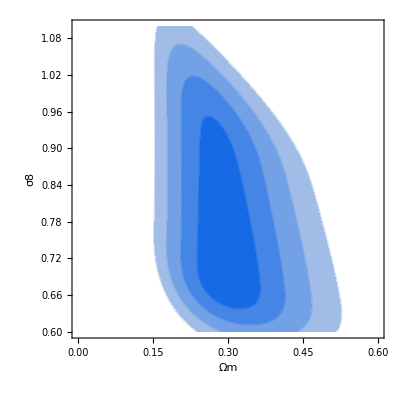

```mathematica
(* 1σ-4σ confidence contour in 2D space (Subscript[Ω, 0m], σ8) , with  marginalization over Subscript[g, a] , including the fiducial correction factor*)

contour2fσ8marg=ContourPlot[chi2fidmarg[datafσ8fid,-1,om,2,σ8],{om,0. ,0.6},{σ8,0.6,1.1},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfσ8marg[[1]]+dchi[1,2],chi2minfσ8marg[[1]]+dchi[2,2],chi2minfσ8marg[[1]]+dchi[3,2],chi2minfσ8marg[[1]]+dchi[4,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]
```

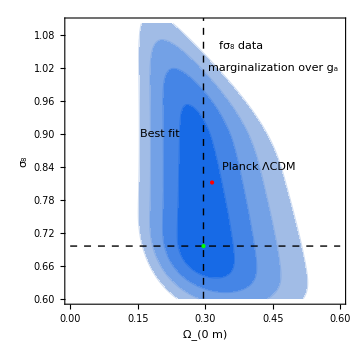

```mathematica
cont2fσ8marg=Show[contour2fσ8marg,Graphics[{Inset["Best fit",{0.2,0.9},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 data",{0.38,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["marginalization over g_a ",{0.45,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{chi2minfσ8marg[[2,1,2]],0.6},{chi2minfσ8marg[[2,1,2]],1.2}}]},{Dashed,Line[{{0.,chi2minfσ8marg[[2,2,2]]},{0.6,chi2minfσ8marg[[2,2,2]]}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfσ8marg[[2,1,2]],chi2minfσ8marg[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

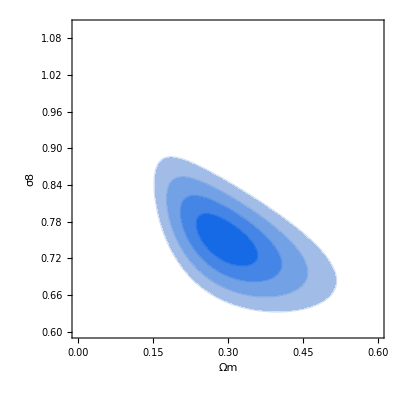

```mathematica
(* 1σ-4σ confidence contour in 2D space (Subscript[Ω, 0m], σ8) (with Subscript[g, a]=0) including the fiducial correction factor*)

contour2fσ8gr=ContourPlot[chi2fid[datafσ8fid,-1,om,0,0,σ8],{om,0. ,0.6},{σ8,0.6,1.1},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfσ8gr[[1]]+dchi[1,2],chi2minfσ8gr[[1]]+dchi[2,2],chi2minfσ8gr[[1]]+dchi[3,2],chi2minfσ8gr[[1]]+dchi[4,2]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],Hue[0.6,.2,.9],Hue[0.6,.1,.9],Hue[0.6,.05,.9],White}]
```

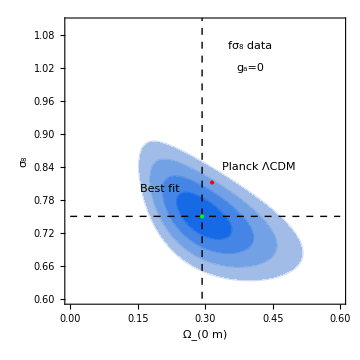

```mathematica
cont2fσ8gr=Show[contour2fσ8gr,Graphics[{Inset["Best fit",{0.2,0.8},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 data",{0.4,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["g_a=0  ",{0.4,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{chi2minfσ8gr[[2,1,2]],0.6},{chi2minfσ8gr[[2,1,2]],1.2}}]},{Dashed,Line[{{0.,chi2minfσ8gr[[2,2,2]]},{0.6,chi2minfσ8gr[[2,2,2]]}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfσ8gr[[2,1,2]],chi2minfσ8gr[[2,2,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

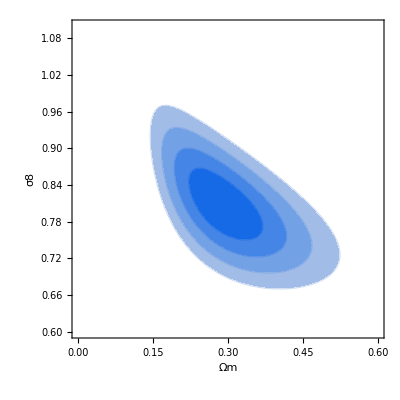

```mathematica
(* 1σ-4σ confidence contour in 2D projected space  (Subscript[Ω, 0m], σ8) of the parameter space (Subscript[Ω, 0m], Subscript[g, a], σ8) including the fiducial correction factor*)

contour2fσ8=ContourPlot[chi2fid[datafσ8fid,-1,om,chi2minfσ8[[2,2,2]],2,σ8],{om,0,0.6},{σ8,0.6,1.1},FrameLabel->{"Ωm","σ8"},Contours->{chi2minfσ8[[1]]+dchi[1,3],chi2minfσ8[[1]]+dchi[2,3],chi2minfσ8[[1]]+dchi[3,3],chi2minfσ8[[1]]+dchi[4,3]},ContourShading->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White},ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.7,.9],Hue[0.6,.5,.9],Hue[0.6,.3,.9],White}]
```

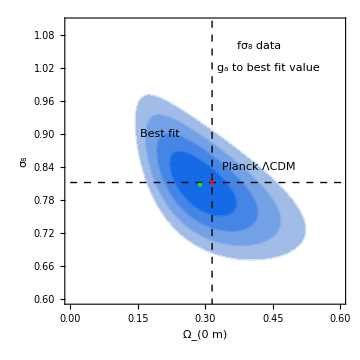

```mathematica
cont2fσ8=Show[contour2fσ8,Graphics[{Inset["Best fit",{0.2,0.9},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",14}]}],Graphics[{Inset["fσ_8 data ",{0.42,1.06},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset[" g_a to best fit value ",{0.44,1.02},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["Planck ΛCDM ",{0.42,0.84},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",14}]}],FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0,0.6},{0.6,1.1}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},Epilog->{{Dashed,Line[{{0.3153,0.4},{0.3153,1.2}}]},{Dashed,Line[{{0,0.8111},{0.8,0.8111}}]},{PointSize[Large],Red,Point[{0.3153,0.8111}]},{PointSize[Large],Green,Point[{chi2minfσ8[[2,1,2]],chi2minfσ8[[2,3,2]]}]}},FrameStyle->Directive[Black,Thick],ImageSize->Medium]
```

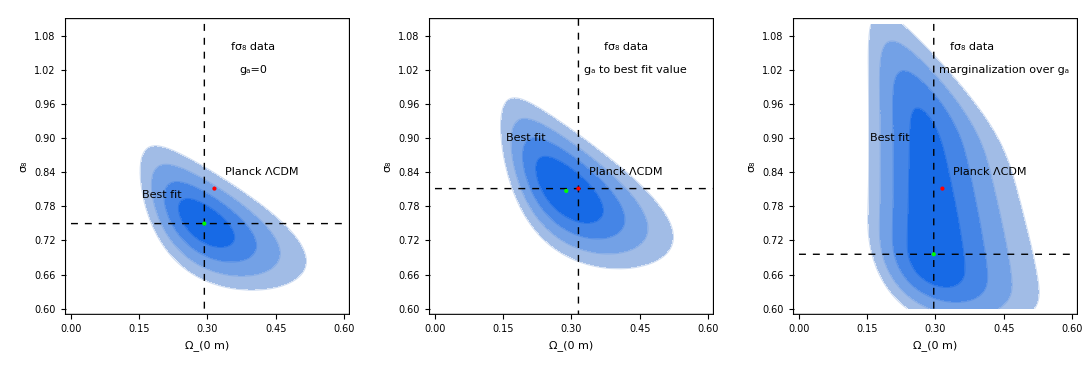

```mathematica
fig8=GraphicsGrid[{{cont2fσ8gr,cont2fσ8,cont2fσ8marg}},Spacings->0]
Export[NotebookDirectory[]<>"fig8sub3.pdf",fig8,ImageResolution->1000];
```